## Rigid, θ1<θ2, q11<q21

```mathematica
g[x_,θ1_,θ2_,q11_,q12_,q21_,q22_]:= (x-q11) (θ1-If[x<=q11,1,0])+(x-q12) (θ2-If[x<=q12,1,0])-(x-q21) (θ1-If[x<=q21,1,0])-(x-q22) (θ2-If[x<=q22,1,0])
```

### case 1: q11<q12<q21<q22

```mathematica
Assumptions->θ1<θ2 && q11<q12<q21<q22 && q11<x<=q12
x==-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2
x== θ1 q11 + (1-θ1) q21 +(1-θ2) (q12-q22)
```

```mathematica
Assumptions->θ1<θ2 && q11<q12<q21<q22 && q21<x<=q22
x==1/2 (q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2)
x==1/2(   θ1 q11 + (1- θ1)q21 +θ2 q12 +(1- θ2)q22)
```

### case 2: q11<q21<q12<q22

```mathematica
Assumptions->θ1<θ2 && q11<q21<q12<q22 && q11<x<=q21
x==-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2
```

```mathematica
Assumptions->θ1<θ2 && q11<q21<q12<q22 && q12<x<=q22
x==q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2
x ==  θ1 (q11 -q21) + θ2 q12 + (1-θ2) q22
```

### case 3: q11<q21<q22<q12

```mathematica
Assumptions->θ1<θ2 && q11<q21<q22<q12 && q11<x<=q21
x==-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2
x== θ1 q11 + (1-θ1) q21 +(1-θ2) (q12-q22)
```

```mathematica
Assumptions->θ1<θ2 && q11<q21<q22<q12&& q22<x<=q12
x==q12-q11 θ1+q21 θ1-q12 θ2+q22 θ2
x==θ1 (q21 -q11) + θ2 q22+(1-θ2) q12
```

### Check if roots exist in the non-constant region

```mathematica
Simplify[q11<=-q12+q21+q22+q11 θ1-q21 θ1+q12 θ2-q22 θ2,Assumptions->0<θ1<θ2<1 && q11<q12<q21<q22]
```

q11+q12+q21 θ1+q22 θ2≤q21+q22+q11 θ1+q12 θ2

## Rigid, θ1<θ2<θ3, q11<q21

```mathematica
g[x_,θ1_,θ2_,θ3_,q11_,q12_,q13_,q21_,q22_,q23_]:= (x-q11) (θ1-If[x<=q11,1,0])+(x-q12) (θ2-If[x<=q12,1,0])+(x-q13) (θ3-If[x<=q13,1,0])-(x-q21) (θ1-If[x<=q21,1,0])-(x-q22) (θ2-If[x<=q22,1,0])-(x-q23) (θ3-If[x<=q23,1,0])
```

### case 1: q11<q21<q12<q22 <q13<q23

```mathematica
Collect[Simplify[g[x,θ1,θ2,q11,q12,q21,q22],Assumptions->θ1<θ2 && q11<q21<q12<q22 && x<=q11],x]
```

q11+q12-q21-q22-q11 θ1+q21 θ1-q12 θ2+q22 θ2

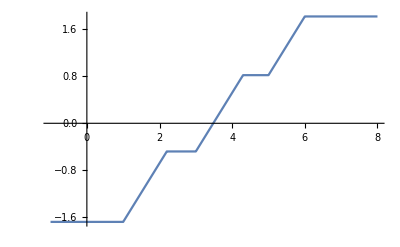

```mathematica
Plot[g[x,0.2,0.6,0.8,1,3,5,2.2,4.3,6],{x,-1,8}]
```

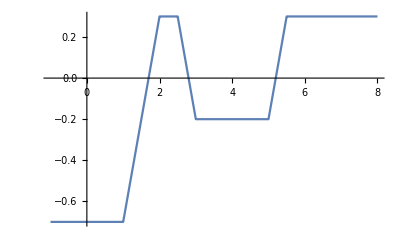

```mathematica
Plot[g[x,0.2,0.6,0.8,1,3,5,2,2.5,5.5],{x,-1,8}]
```

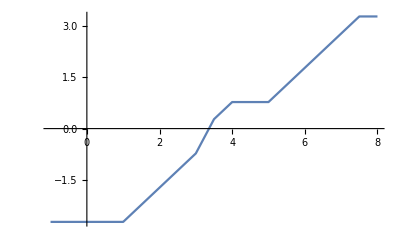

```mathematica
Plot[g[x,0.2,0.3,0.99,1,3,5,3.5,4,7.5],{x,-1,8}]
```

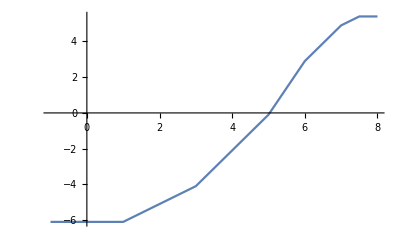

```mathematica
Plot[g[x,0.2,0.6,0.8,1,3,5,6,7,7.5],{x,-1,8}]
```